Starting point is (4.27) written here with N=lna. In matter domination we have conformal H^2= H_0^2 exp(-lna). The linear version of the equation has the solution

```mathematica
DSolve[plin''[lna]+3/2(1-2w)plin'[lna]-(9 w)/2 plin[lna]== -3w ψlin,plin[lna],lna]
```

{{plin[lna]→(2 ψlin)/3+ⅇ^(3 lna w) C[1]+ⅇ^(-3 lna/2) C[2]}}

We recognize that plin -> 2/3 ψ where plin is the linear part of pi-tilde. Let us now consider the spherically symmetric quadratic potential, that is
ψ(r) = ψ_0 + ψ_2 r^2
where in matter domination we assume ψ = constant (pi-tilde will be treated as a spectator field). We can now construct a solution to the nonlinear equation by writing
π̃= 2/3 ψ(r) + r^2 p2(lna)
Evidently p2(lna) is a second-order correction. The purely second-order solution can be found by solving the second-order part of (4.27) which gives

```mathematica
DSolve[p2''[lna]+3/2(1-2w)p2'[lna]-(9w)/2 p2[lna]+ (2+3w)/H0^2 Exp[lna] 8/9 ψ2^2== 0,p2[lna], lna]//Simplify
```

{{p2[lna]→(16 ⅇ^lna (2+3 w) ψ2^2)/(45 H0^2 (-1+3 w))+ⅇ^(3 lna w) C[1]+ⅇ^(-3 lna/2) C[2]}}

This shows that p2(lna) goes to a particular solution at early times. This fixes our initial condition for p2(lna) for the fully non-linear solution. To compute it, we need to pick some parameters:

```mathematica
{3/2(1-2w),-(9 w)/2,(2+3w)/H0^2,(16 ⅇ^lna (2+3 w) ψ2^2)/(45 H0^2 (-1+3 w))}/.w-> -9/10/.H0-> 1
```

{21/5,81/20,-7/10,(112 ⅇ^lna ψ2^2)/1665}

Note that setting H0 = 1 effectively means that ψ_2 = ψ'' / 2 H_0^2. Let us scan through a few values...

```mathematica
nsoltab=Table[NDSolve[{p2''[lna]+21/5 p2'[lna]+81/20 p2[lna] - 7/10 Exp[lna](8/9 ψ2^2+8/3 ψ2 p2[lna]+2 p2[lna]^2)== 0, p2[-10]== (112 ψ2^2)/1665 Exp[-10],p2'[-10]== (112 ψ2^2)/1665 Exp[-10]}/.ψ2-> 2^n,p2,{lna,-10,10}],{n,-3,2}]
```

{{{p2→InterpolatingFunction[…]}},{{p2→InterpolatingFunction[…]}},{{p2→InterpolatingFunction[…]}},{{p2→InterpolatingFunction[…]}},{{p2→InterpolatingFunction[…]}},{{p2→InterpolatingFunction[…]}}}

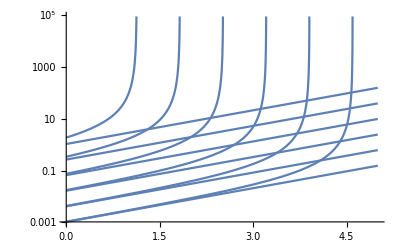

```mathematica
LogPlot[Join[Table[(112 ⅇ^lna ψ2^2)/1665/.ψ2-> 2^n,{n,-3,2}],Flatten[p2[lna]/.nsoltab]],{lna,0,5}]
```

I read off the blowup lna and tabulate it versus the curvature of the potential:

```mathematica
blowup={{Log[1/8],4.6},{Log[1/4],3.9},{Log[1/2],3.21},{Log[1],2.52},{Log[2],1.82},{Log[4],1.13}};
```

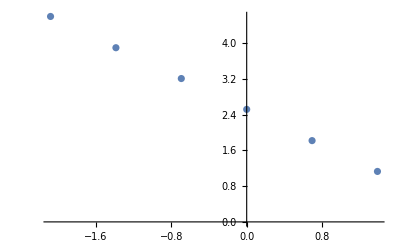

```mathematica
ListPlot[blowup]
```

```mathematica
Fit[blowup,{x,1},x]
```

2.51648-1.00082 x

```mathematica
(2 Gamma[1/3]Gamma[7/6])/(√π)//N
```

2.80436

```mathematica
2.804364210650909 (3/8)^3(2)^(1/3)//N
```

0.186325